### Einführendes Beispiel: Mathematisches Pendel als Taktmechanismus

#### 1. Schritt:

Numerisches Lösen der nichtlinearen DGL 2. Ordnung für einen gegebenen Startwert φ_0:

```mathematica
g=9.81;
l=0.6;
```

```mathematica
φp[t_,φ0_]:=φ[t]/.First[NDSolve[{φ''[t]==-g/l Sin[φ[t]],φ[0]==φ0,φ'[0]==0},φ[t],{t,0,40}]]
```

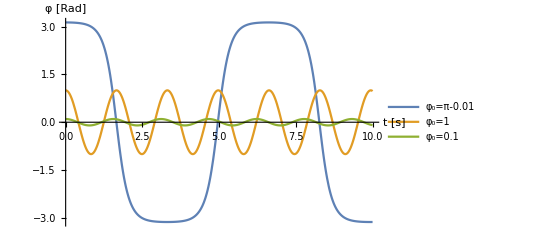

```mathematica
Plot[Evaluate[{φp[t,π -.01],φp[t,1],φp[t,.1]}],{t,0,10},PlotLegends->{"φ_0=π-0.01","φ_0=1","φ_0=0.1"},AxesLabel->{"t [s]","φ [Rad]"},LabelStyle->Medium,PlotStyle->Thick]
```

#### 2. Schritt:

Berechnen der Periodizität T

```mathematica
T[φ0_,T0_]:=4 t/.FindRoot[φp[t,φ0]==0,{t,T0}]
```

Startwertfunktion für Berechnung des Nulldurchgangs (Startwert für die Newton-Methode):

```mathematica
T0[φ0_]:=Piecewise[{{.1,φ0≤1},{.1+(φ0-1) 0.9/(π-1),φ0>1}}]
```

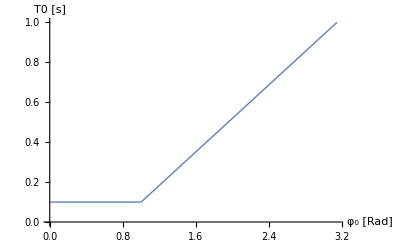

```mathematica
Plot[T0[φ0],{φ0,0,π},AxesLabel->{"φ_0 [Rad]","T0 [s]"},LabelStyle->Medium,PlotStyle->Thick]
```

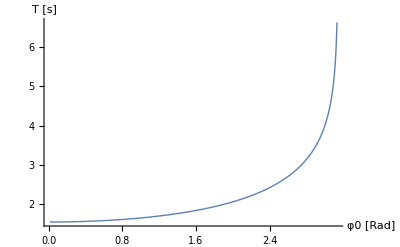

```mathematica
Plot[T[φ0,T0[φ0]],{φ0,0.01,π-.01},AxesLabel->{"φ0 [Rad]","T [s]"},PlotRange->All,LabelStyle->Medium,PlotStyle->Thick]
```

Linearisierte DGL:

```mathematica
DSolve[{φ''[t]==-g0/l0 φ[t],φ[0]==φ0,φ'[0]==0},φ[t],t]
```

{{φ[t]→φ0 Cos[(√g0 t)/(√l0)]}}

Die Lösung hat eine von φ_0unabhängige Periodizität! Die Linearisierung des mathematischen Modells ist für die Aufgabenstellung nicht zulässig.

```mathematica
Tmin=T/.Solve[2π 1/T==√(g0/l0),T][[1]]/.{g0->g,l0->l}
```

1.55389

#### 3. Schritt: φ_0(T)

Effektiv gesucht ist φ_0(T) und nicht T(φ_0), daher muss die Inverse von T(φ_0) berechnet werden. Die Aufgabe wird hier graphisch gelöst:

```mathematica
f[φ0_?NumberQ]:=T[φ0,T0[φ0]]
```

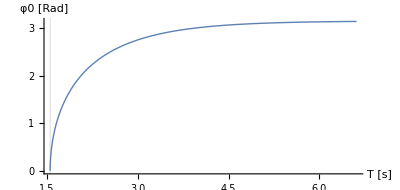

```mathematica
ParametricPlot[{f[φ0],φ0},{φ0,0.01,π-.01},AxesLabel->{"T [s]","φ0 [Rad]"},PlotRange->All,AxesOrigin->{0,0},AspectRatio->π/T[π-.01,T0[π-.01]],GridLines->{{Tmin},None},LabelStyle->Medium,PlotStyle->Thick]
```

#### Kompakt in Mathematica:

Die obige Vorgehensweise führt nicht zu einem sehr robusten numerischen Verfahren. Robuster ist der Ansatz, die DGL numerisch nur bis zu einem Vorzeichenwechsel zu lösen. Entsprechend erhält man direkt die Periodizität aus dem DGL-Solver. In Mathematica kann dies mit Hilfe von Events umgesetzt werden:

```mathematica
f[φ0_?NumberQ]:=Module[{p=0},NDSolve[{φ''[t]==-g/l Sin[φ[t]],φ[0]==φ0,φ'[0]==0},φ,{t,∞},Method->{"EventLocator","Event"->φ[t],"EventAction":>Throw[p=t,"StopIntegration"]}];
4p];
```

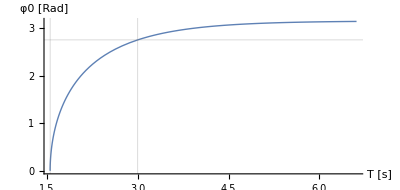

```mathematica
ParametricPlot[{f[φ0],φ0},{φ0,0.01,π-.01},AxesLabel->{"T [s]","φ0 [Rad]"},PlotRange->All,AxesOrigin->{0,0},AspectRatio->π/T[π-.01,T0[π-.01]],GridLines->{{Tmin,3},{φ0/.Evaluate[FindRoot[f[φ0]==3,{φ0,π-10^-4}]]}},LabelStyle->Medium,PlotStyle->Thick]
```

Numerische Berechnung des Startwinkels bei gegebener Periodizität:

```mathematica
FindRoot[f[φ0]==3,{φ0,π-10^-4}]
```

{φ0→2.74578}